# PHAS2443 2015 exam Hayk Khachatryan

## Section A

### Question 1

```mathematica
fib[1] = 0
fib[2] =1
fib[n_] := fib[n-1] + fib[n-2]

Table[fib[i], {i, 1, 25}]
```

0

1

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368}

### Question 2

```mathematica
sin[x_, m_] := Sum[(-1)^k x^(2k+1)/((2k+1)!), {k, 0, m}]
```

```mathematica
m2 = Abs[sin[π/4, 2]-Sin[π/4]]//N
m4 = Abs[sin[π/4, 4] - Sin[π/4]]//N
m8 = Abs[sin[π/4, 8]- Sin[π/4]]//N
m16 = Abs[sin[π/4,16]- Sin[π/4]]  //N
```

0.0000362646

1.75032×10^-9

4.2172×10^-17

4.20886×10^-17

```mathematica
{Log10[m2], Log10[m4], Log10[m8], Log10[m16]}
```

{-4.44052,-8.75688,-16.375,-16.3758}

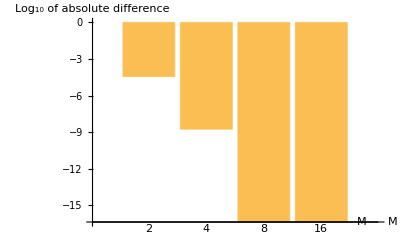

```mathematica
BarChart[{Log10[m2], Log10[m4], Log10[m8], Log10[m16]}, ChartLabels-> {"2", "4", "8","16"}, AxesLabel->{"M", "Log_10 of absolute difference"}]
```

The higher the M the smaller the difference between sinx and our approximation, though after M = 8 the difference is negligible

### Question 3

```mathematica
k = 1.55 10^-6
eq = {r''[t] == -k/r[t]^2}
bc = {r'[0] == 0, r[0] ==3}
```

1.55×10^-6

{r''[t]==-(1.55×10^-6)/r[t]^2}

{r'[0]==0,r[0]==3}

```mathematica
sol = NDSolve[
Join[eq, bc],
r[t],
{t, 0, 4500}]
```

{{r[t]→InterpolatingFunction[{{0., 4500.}}, <>][t]}}

```mathematica
r1 = (r[t] /. sol)[[1]] == 1
```

InterpolatingFunction[{{0., 4500.}}, <>][t]==1

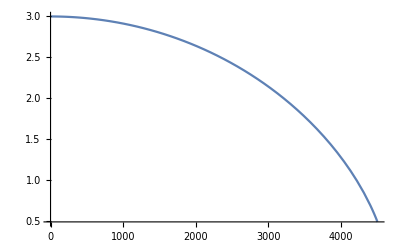

```mathematica
Plot[ r[t] /. sol, {t, 0, 4500}]
```

```mathematica
FindRoot[
r1,
{t, 4000}]
```

{t→4210.56}

### Question 4

```mathematica
perfect[n_] := Total[Divisors[n][[;;-2]]] == n
```

```mathematica
Select[Range[10000], perfect[#] &]
```

{6,28,496,8128}

### Question 5

```mathematica
dj = Table[2Sin[2π j/20]+RandomReal[{-0.5,0.5}], {j, 1, 200}]
```

{1.02067,1.60825,1.22092,2.31382,2.3882,2.21717,1.28718,0.887171,0.472922,0.483655,-0.150777,-1.11494,-1.22723,-1.48594,-2.25979,-2.19889,-2.1038,-1.0592,-0.811857,-0.443607,0.347094,1.6611,1.57656,1.7928,2.36109,2.16788,1.67193,1.61777,0.414311,0.205391,-0.444774,-1.20566,-2.03195,-1.55804,-2.17034,-1.90337,-1.94887,-1.6429,-0.620795,0.455217,0.711067,0.759511,1.9345,1.80477,2.04174,2.04684,1.3934,0.925267,0.599042,-0.334414,-0.924618,-1.05742,-1.43153,-2.05922,-2.05048,-2.39749,-1.94122,-1.43732,-1.04372,-0.271375,0.71667,1.31214,1.90336,1.51199,2.10732,2.07642,1.25353,1.60513,0.419006,0.378369,-0.784376,-1.58722,-1.23683,-2.19986,-2.3054,-1.58071,-1.21526,-1.24662,-0.270813,-0.499401,0.199078,0.766829,1.65335,1.94444,2.06951,1.82435,1.39371,0.819761,0.922848,0.299398,-1.08644,-0.70616,-1.28962,-1.63083,-2.2804,-1.43509,-1.33633,-0.993927,-0.380593,0.0444434,0.725187,1.46499,1.58106,1.40733,2.05825,1.81197,1.79794,1.27251,0.784851,0.248699,-0.226344,-1.47514,-2.04712,-2.31085,-1.88782,-1.68254,-1.74962,-1.11664,-0.173718,0.234487,1.11268,1.20917,1.49778,1.62708,2.03073,2.15539,1.56966,1.36663,0.36457,-0.111734,-0.284658,-1.23293,-1.7364,-2.06148,-1.7321,-1.79009,-1.59282,-0.683957,-0.677777,0.243969,0.815885,1.38501,1.60657,1.41232,2.33292,2.29924,1.16175,1.60131,0.921769,-0.363981,-0.402562,-0.989108,-1.60205,-2.32678,-2.37955,-2.09594,-1.83485,-1.51669,-1.02899,0.45024,0.603753,1.15472,1.72174,2.34926,2.08415,1.83641,1.20171,1.05763,0.317795,0.27203,-0.320014,-0.905312,-1.68607,-1.67181,-1.56674,-1.90721,-1.67601,-1.64043,-0.646586,-0.00536545,0.842753,1.25122,1.51719,2.20481,2.42852,1.88173,1.49872,1.11531,0.928171,0.390158,-0.184382,-1.32363,-1.81693,-1.76187,-2.10483,-1.48932,-1.2275,-1.0573,-0.378506,0.32551}

```mathematica
cdj  = ListConvolve[
{0.2,0.2,0.2,0.2,0.2},
dj, 1, 0]
```

{0.204135,0.525784,0.769969,1.23273,1.71037,1.94967,1.88546,1.81871,1.45053,1.06962,0.59603,0.115605,-0.307275,-0.699048,-1.24774,-1.65736,-1.85513,-1.82152,-1.68671,-1.32347,-0.814274,-0.0612946,0.465858,0.98679,1.54773,1.91189,1.91405,1.92229,1.64659,1.21546,0.692925,0.117407,-0.612536,-1.00701,-1.48215,-1.77387,-1.92251,-1.8447,-1.65726,-1.13214,-0.609257,-0.0675801,0.6479,1.13301,1.45032,1.71747,1.84425,1.6424,1.40126,0.926028,0.331736,-0.158429,-0.629788,-1.16144,-1.50465,-1.79923,-1.97599,-1.97715,-1.77405,-1.41823,-0.795394,-0.144722,0.523415,1.03456,1.5103,1.78225,1.77053,1.71088,1.49228,1.14649,0.574332,0.00618026,-0.562211,-1.08598,-1.62274,-1.782,-1.70761,-1.70957,-1.32376,-0.962561,-0.606603,-0.210186,0.369808,0.81286,1.32664,1.6517,1.77707,1.61036,1.40604,1.05201,0.469856,0.0498813,-0.371995,-0.882731,-1.39869,-1.46842,-1.59445,-1.53531,-1.28527,-0.820298,-0.388244,0.172019,0.687017,1.0446,1.44736,1.66472,1.73131,1.6696,1.5451,1.18319,0.775531,0.120915,-0.54301,-1.16215,-1.58946,-1.88069,-1.93559,-1.74949,-1.32207,-0.897605,-0.338561,0.253196,0.77608,1.13624,1.49549,1.70403,1.77613,1.7499,1.4974,1.0689,0.580895,0.0203766,-0.60023,-1.08544,-1.40951,-1.7106,-1.78258,-1.57209,-1.29535,-0.900136,-0.378941,0.216626,0.674732,1.09275,1.51054,1.80721,1.76256,1.76151,1.6634,1.12402,0.583657,0.153486,-0.487186,-1.1369,-1.54001,-1.87868,-2.04783,-2.03076,-1.7712,-1.20525,-0.665308,-0.0673942,0.580292,1.25594,1.58272,1.82926,1.83865,1.70583,1.29954,0.937115,0.50583,0.0844252,-0.464314,-0.862235,-1.22999,-1.54743,-1.70157,-1.69244,-1.4874,-1.17512,-0.625128,-0.0396804,0.591843,1.16212,1.6489,1.85669,1.90619,1.82582,1.57049,1.16282,0.749594,0.185124,-0.401324,-0.939332,-1.43833,-1.69932,-1.68009,-1.52817,-1.25149,-0.765424}

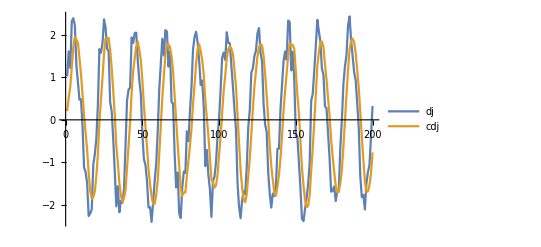

```mathematica
ListPlot[{dj, cdj}, Joined -> True, PlotLegends -> {"dj", "cdj"}]
```

### Question 6

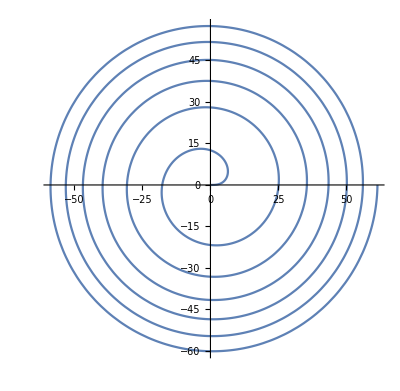

```mathematica
PolarPlot[10Sqrt[θ], {θ, 0, 12π}]
```

```mathematica
r[θ_] := 10 Sqrt[θ]

ParametricPlot[{r[θ] Cos[θ], r[θ] Sin[θ]}, {θ, 0, 12π}]
```

-Graphics-

```mathematica
θs = Table[n π(3-√5), {n, 1, 15}]
```

{(3-√5) π,2 (3-√5) π,3 (3-√5) π,4 (3-√5) π,5 (3-√5) π,6 (3-√5) π,7 (3-√5) π,8 (3-√5) π,9 (3-√5) π,10 (3-√5) π,11 (3-√5) π,12 (3-√5) π,13 (3-√5) π,14 (3-√5) π,15 (3-√5) π}

```mathematica
{θ -> #} & /@ θs
```

{{θ→(3-√5) π},{θ→2 (3-√5) π},{θ→3 (3-√5) π},{θ→4 (3-√5) π},{θ→5 (3-√5) π},{θ→6 (3-√5) π},{θ→7 (3-√5) π},{θ→8 (3-√5) π},{θ→9 (3-√5) π},{θ→10 (3-√5) π},{θ→11 (3-√5) π},{θ→12 (3-√5) π},{θ→13 (3-√5) π},{θ→14 (3-√5) π},{θ→15 (3-√5) π}}

```mathematica
news = {r[θ] Cos[θ], r[θ] Sin[θ]} /. {θ -> #} & /@ θs
```

{{10 √((3-√5) π) Cos[(3-√5) π],10 √((3-√5) π) Sin[(3-√5) π]},{10 √(2 (3-√5) π) Cos[2 (3-√5) π],10 √(2 (3-√5) π) Sin[2 (3-√5) π]},{10 √(3 (3-√5) π) Cos[3 (3-√5) π],10 √(3 (3-√5) π) Sin[3 (3-√5) π]},{20 √((3-√5) π) Cos[4 (3-√5) π],20 √((3-√5) π) Sin[4 (3-√5) π]},{10 √(5 (3-√5) π) Cos[5 (3-√5) π],10 √(5 (3-√5) π) Sin[5 (3-√5) π]},{10 √(6 (3-√5) π) Cos[6 (3-√5) π],10 √(6 (3-√5) π) Sin[6 (3-√5) π]},{10 √(7 (3-√5) π) Cos[7 (3-√5) π],10 √(7 (3-√5) π) Sin[7 (3-√5) π]},{20 √(2 (3-√5) π) Cos[8 (3-√5) π],20 √(2 (3-√5) π) Sin[8 (3-√5) π]},{30 √((3-√5) π) Cos[9 (3-√5) π],30 √((3-√5) π) Sin[9 (3-√5) π]},{10 √(10 (3-√5) π) Cos[10 (3-√5) π],10 √(10 (3-√5) π) Sin[10 (3-√5) π]},{10 √(11 (3-√5) π) Cos[11 (3-√5) π],10 √(11 (3-√5) π) Sin[11 (3-√5) π]},{20 √(3 (3-√5) π) Cos[12 (3-√5) π],20 √(3 (3-√5) π) Sin[12 (3-√5) π]},{10 √(13 (3-√5) π) Cos[13 (3-√5) π],10 √(13 (3-√5) π) Sin[13 (3-√5) π]},{10 √(14 (3-√5) π) Cos[14 (3-√5) π],10 √(14 (3-√5) π) Sin[14 (3-√5) π]},{10 √(15 (3-√5) π) Cos[15 (3-√5) π],10 √(15 (3-√5) π) Sin[15 (3-√5) π]}}

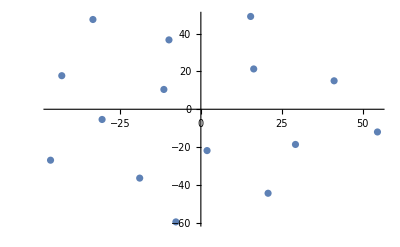

15

```mathematica
ListPlot[news]
Length[news]
```

## Section B

### Question 7

```mathematica
p[x_] := (1+ Cos[x])/(2+π)
```

```mathematica
f[x_, p_, a_] := Integrate[p[b], {b, a, x}]
```

```mathematica
f[x, p, -π/2]
```

(2+π+2 x+2 Sin[x])/(4+2 π)

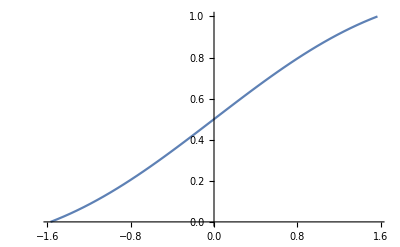

```mathematica
Plot[f[x,p,-π/2], {x, -π/2,π/2}]
```

```mathematica
fSolver[r_] := 
FindRoot[
f[x, p, -π/2] == r,
{x, r π-π/2}
]
```

```mathematica
fSolver[r, r π-π/2]
```

fSolver[r,-π/2+π r]

```mathematica
fSolver[0.4]
```

{x→-0.258515}

```mathematica
x/.{x->1.5707963267948966}
```

1.5708

```mathematica
SeedRandom[2015]
```

```mathematica
R = Table[RandomReal[], 2000];
```

```mathematica
X1 = {}
Timing[Do[
AppendTo[X1,x/. fSolver[r]],
{r, R}]]
```

{}

{77.6406,Null}

Histogram::hbins: The bin specification 0.2 cannot be used to determine either how many or which bins to use.

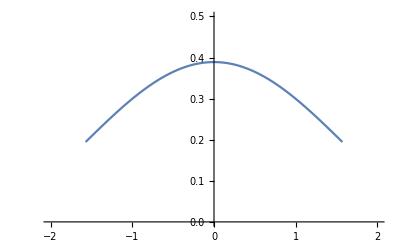

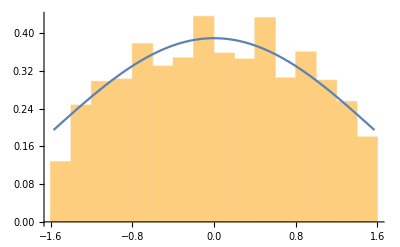

```mathematica
h = Histogram[X1, 0.2, "PDF"];
plot = Plot[p[x], {x, -π/2,π/2}, PlotRange->{{-2,2},{0,0.5}}]

Show[h,plot]
```

```mathematica
nSolver[r_]:=
Module[
{x0},
x0 = r π - π/2;

NestWhile[
# + (r-f[#, p, -π/2])/p[#] &,
x0,
Abs[{##}[[1]] - {##}[[2]]] > 10^-4 &,
2]]
```

```mathematica
X2 = {}

Timing[Do[
AppendTo[X2, nSolver[r]], {r, R}]]
```

{}

{29.5625,Null}

```mathematica
xDiff = MapThread[
Abs[#1-#2] &,
{X1, X2}];
```

```mathematica
SortBy[MapThread[
{#1, #2} &, {R, xDiff}], First]
```

{{0.00168224,1.50311×10^-11},{0.00206309,3.35181×10^-11},{0.00233953,5.48532×10^-11},{0.00260403,8.336×10^-11},1992,{0.995876,4.95506×10^-10},{0.996941,1.5612×10^-10},{0.996943,1.55647×10^-10},{0.997694,5.18587×10^-11}}
 |  |  |  |

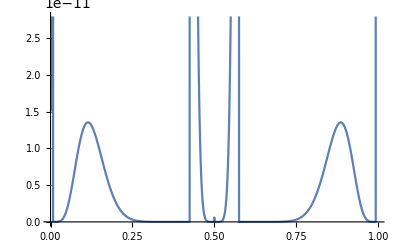

```mathematica
ListPlot[SortBy[MapThread[
{#1, #2} &, {R, xDiff}], First], Joined->True]
```

### Question 8

```mathematica
s = Table[0, 601];

s[[300]]  = 1
```

1

```mathematica
rules = {{0,0,0} -> 0, {0,0,1} -> 1, {0,1,0} -> 1, {0,1,1} -> 1, {1,0,0} -> 1, {1,0,1} -> 0, {1,1,0} -> 0, {1,1,1} -> 0}
```

{{0,0,0}→0,{0,0,1}→1,{0,1,0}→1,{0,1,1}→1,{1,0,0}→1,{1,0,1}→0,{1,1,0}→0,{1,1,1}→0}

```mathematica
Clear[upd]

upd[list_,rule_] := 
Transpose[{RotateRight[list], list, RotateLeft[list]}] /. rule
```

```mathematica
ArrayPlot[NestList[upd[#, rules] & , s, 300]]
```

-Graphics-

```mathematica
d = Table[0, 31,31];

d[[16,16]]  = 1 ;

d//ArrayPlot
```

-Graphics-

```mathematica
r[a_,b_,c_] := {a,b,c} /. rules
```

```mathematica
Clear[upd]

upd[list_] := 
Module[
{lp},
lp = list;

Do[
lp[[i,j]] = 
r[
r[
list[[i+1, j-1]],
list[[i+1, j]],
list[[i+1, j+1]]
],
r[
list[[i,j-1]],
list[[i,j]],
list[[i,j+1]]
],
r[
list[[i-1,j-1]],
list[[i-1,j]],
list[[i-1,j+1]]
]
],
{i, 2, 30},
{j,2,30}];
lp]
```

```mathematica
nL = NestWhileList[upd[#] &, d, UnsameQ,2];
ArrayPlot[nL[[-1]]]
Length[nL]
```

-Graphics-

88

```mathematica
upd[list_] :=
Module[
{lp},
lp = list;

Do[
lp[[i,j]] = {{lp[[i+1,j-1]], lp[[i+1,j]], lp[[i+1, j+1]]} /. rules , {lp[[i, j-1]], lp[[i,j]], lp[[i, j+1]]} /. rules, {lp[[i-1, j-1]], lp[[i-1, j]], lp[[i-1, j+1]]} /. rules} /. rules,
{i, 2, 30},
{j, 2, 30}];
lp]
```

### Question 9

```mathematica
n = 100

Δx := 1/n
x = Table[(i-1)/n, {i, 1, n}]
```

100

{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100}

```mathematica
f = Table[Sin[2π i], {i, x}];
```

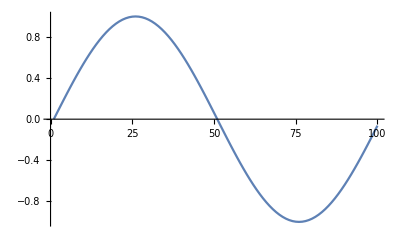

```mathematica
ListPlot[f, Joined -> True]
```

```mathematica
upd[list_]:= 
Module[
{lp},
lp = list;

Do[
lp[[i,
```

### Question 10

```mathematica
Clear[u,a,x,y,z,J2]
u[x_,y_,z_, J2_] := -1/Sqrt[x^2+y^2+z^2]+J2/(2 Sqrt[x^2+y^2+z^2]^3)(3 z/Sqrt[x^2+y^2+z^2]-1)

a[{xx_,yy_,zz_},J2_]:= {-D[u[x,y,z,J2], x], -D[u[x,y,z,J2], y], -D[u[x,y,z,J2], z]} /. {x-> xx, y-> yy, z-> zz}
```

```mathematica
Clear[upd]

upd[{r_, v_}] := 
Module[
{vP, rP},

vP = v + Δt a[r, J2] ;
rP = r + Δt vP;

{rP, vP}]
```

```mathematica
J2 = 0
Δt = 0.1

traj = NestList[
upd,
{{5,0,0}, {0,0.3, 0.3}},
10000]
```

0

0.1

{{{5,0,0},{0,0.3,0.3}},{{4.9996,0.03,0.03},{-0.004,0.3,0.3}},9997,{{-3.45002,1.62438,1.62438},{-0.265815,-0.309626,-0.309626}},{{-3.47612,1.59319,1.59319},{-0.26097,-0.311907,-0.311907}}}
 |  |  |  |

```mathematica
ListPointPlot3D[Transpose[traj][[1]]]
```

-Graphics3D-

```mathematica
vs = Transpose[traj][[2]]
```

{{0,0.3,0.3},{-0.004,0.3,0.3},{-0.00800021,0.299976,0.299976},{-0.0120004,0.299928,0.299928},9993,{-0.275367,-0.304946,-0.304946},{-0.270614,-0.307306,-0.307306},{-0.265815,-0.309626,-0.309626},{-0.26097,-0.311907,-0.311907}}
 |  |  |  |

```mathematica
vupd[list_]:=0.5(RotateRight[list]+ RotateLeft[list])
```

```mathematica
vs = Norm /@ upda[Transpose[traj][[2]]]
rs = Norm /@ Transpose[traj][[1]]
```

{0.132752,0.424266,0.424289,0.424315,0.424345,0.424379,0.424417,0.424458,0.424503,0.424552,9981,0.509806,0.510124,0.510437,0.510746,0.511049,0.511347,0.511639,0.511927,0.512209,0.133082}
 |  |  |  |

{5,4.99978,4.99952,4.99922,4.99888,4.9985,4.99808,4.99762,4.99712,4.99658,4.996,9979,4.16873,4.16589,4.16309,4.16035,4.15764,4.15499,4.15238,4.14983,4.14732,4.14486,4.14245}
 |  |  |  |

```mathematica
e = vs^2/2-1/rs
```

{-0.191188,-0.110008,-0.110009,-0.11001,-0.11001,-0.110011,-0.110012,-0.110013,-0.110014,-0.110014,9982,-0.110093,-0.110092,-0.11009,-0.110089,-0.110088,-0.110087,-0.110085,-0.110084,-0.232548}
 |  |  |  |

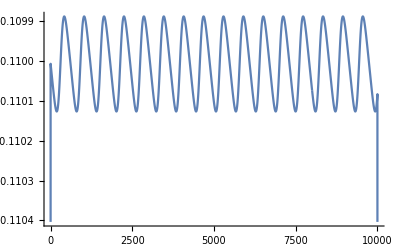

```mathematica
ListPlot[e, Joined->True]
```

```mathematica
Mean[e]
Variance[e]
```

-0.11003

2.16687×10^-6

```mathematica
J2 = 0.05

traj2 = NestList[
upd,
{{5,0,0}, {0,0.3, 0.3}},
10000];
```

0.05

```mathematica
ListPointPlot3D[Transpose[traj2][[1]]] /. Point -> Line
```

-Graphics3D-

### Question 11

```mathematica
Clear[Δt]
```

```mathematica
ω1 := 2 π/(3.5 Δt)
ω2 := 2 π/(5.5 Δt)

n = 128
Δt = 1
```

128

1

```mathematica
d = Table[Cos[ω1 j Δt] +Cos[ω2 j Δt] +RandomReal[{-.5, .5}], {j, 1, n}]
```

{0.212415,-1.45253,-0.807437,0.140271,-0.300997,1.02991,0.874107,-1.19454,-1.70429,1.09292,1.48336,-0.952287,-0.888894,-0.143538,-0.00113192,-0.148188,1.96083,0.903224,-2.27433,-1.31421,1.16655,0.45313,-0.0725513,-0.379003,-0.783655,-0.604218,0.62228,1.96919,0.0822474,-1.68884,0.0424942,0.615644,-0.157036,-0.144702,0.565856,-1.30589,-0.707141,1.56424,1.60147,-1.02872,-0.79459,0.481903,0.512616,0.527481,1.01519,-0.142156,-2.03276,-0.154269,1.42379,0.88549,-1.38465,-0.274203,-0.186394,-0.10425,0.957788,1.38533,-1.01227,-1.99195,0.337701,1.03706,-0.0244773,0.103675,0.373594,-0.61274,-0.311306,1.33334,0.758392,-1.75969,-1.64121,0.694915,0.814724,0.128469,0.563797,-0.145914,-1.77191,0.623915,1.54559,0.417964,-1.7459,-0.364722,0.969918,-0.428294,0.568442,0.450153,-0.888462,-1.54744,1.04681,1.69417,-0.121208,-0.857527,0.399684,-0.166674,-0.454065,1.50421,0.920086,-1.73379,-0.690413,0.927618,0.419066,-0.899318,-0.423353,0.155676,-1.53399,0.369843,1.53842,-0.480971,-1.94978,-0.235123,1.42663,0.533421,-0.1825,0.823672,-1.3028,-0.792909,1.45259,1.18962,-1.13101,-1.27135,0.541092,-0.0528381,0.360627,0.930942,-0.323304,-2.11053,-0.131481,1.95033,0.95314,-0.771375}

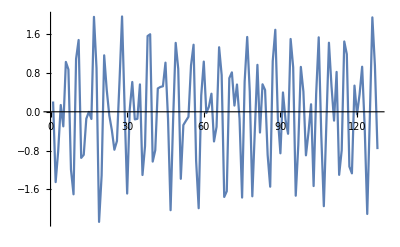

```mathematica
p1 = ListPlot[d, Joined->True]
```

```mathematica
Abs[Fourier[d]]
```

{0.137972,0.232957,0.148362,0.244973,0.179269,0.368707,0.111986,0.229781,0.530026,0.18355,0.155699,0.520207,0.392904,0.316062,0.659489,0.0351246,0.693475,0.418356,0.258499,0.0342346,0.738484,0.990411,1.13147,4.81392,1.91152,0.858303,0.765628,0.463888,0.360658,0.253615,0.37332,0.636347,0.714507,0.588246,0.664654,1.02951,3.13253,3.87703,1.56659,0.748008,0.569059,0.430666,0.27284,0.156333,0.297927,0.350287,0.426713,0.397093,0.286992,0.360741,0.204217,0.315868,0.469359,0.534875,0.278028,0.289788,0.140554,0.148418,0.491646,0.360621,0.433658,0.299422,0.273435,0.27272,0.0983751,0.27272,0.273435,0.299422,0.433658,0.360621,0.491646,0.148418,0.140554,0.289788,0.278028,0.534875,0.469359,0.315868,0.204217,0.360741,0.286992,0.397093,0.426713,0.350287,0.297927,0.156333,0.27284,0.430666,0.569059,0.748008,1.56659,3.87703,3.13253,1.02951,0.664654,0.588246,0.714507,0.636347,0.37332,0.253615,0.360658,0.463888,0.765628,0.858303,1.91152,4.81392,1.13147,0.990411,0.738484,0.0342346,0.258499,0.418356,0.693475,0.0351246,0.659489,0.316062,0.392904,0.520207,0.155699,0.18355,0.530026,0.229781,0.111986,0.368707,0.179269,0.244973,0.148362,0.232957}

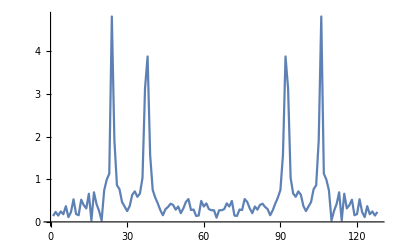

```mathematica
ListPlot[Partition[Riffle[Range[n], Abs[Fourier[d]]],2], Joined->True, PlotRange->All]
```

```mathematica
ωs = Join[Table[2 π/n(k-1), {k, 1, n/2+1}], Table[-2 π/n(n+1-k), {k, n/2+2, n}]]
```

{0,π/64,π/32,(3 π)/64,π/16,(5 π)/64,(3 π)/32,(7 π)/64,π/8,(9 π)/64,(5 π)/32,(11 π)/64,(3 π)/16,(13 π)/64,(7 π)/32,(15 π)/64,π/4,(17 π)/64,(9 π)/32,(19 π)/64,(5 π)/16,(21 π)/64,(11 π)/32,(23 π)/64,(3 π)/8,(25 π)/64,(13 π)/32,(27 π)/64,(7 π)/16,(29 π)/64,(15 π)/32,(31 π)/64,π/2,(33 π)/64,(17 π)/32,(35 π)/64,(9 π)/16,(37 π)/64,(19 π)/32,(39 π)/64,(5 π)/8,(41 π)/64,(21 π)/32,(43 π)/64,(11 π)/16,(45 π)/64,(23 π)/32,(47 π)/64,(3 π)/4,(49 π)/64,(25 π)/32,(51 π)/64,(13 π)/16,(53 π)/64,(27 π)/32,(55 π)/64,(7 π)/8,(57 π)/64,(29 π)/32,(59 π)/64,(15 π)/16,(61 π)/64,(31 π)/32,(63 π)/64,π,-(63 π)/64,-(31 π)/32,-(61 π)/64,-(15 π)/16,-(59 π)/64,-(29 π)/32,-(57 π)/64,-(7 π)/8,-(55 π)/64,-(27 π)/32,-(53 π)/64,-(13 π)/16,-(51 π)/64,-(25 π)/32,-(49 π)/64,-(3 π)/4,-(47 π)/64,-(23 π)/32,-(45 π)/64,-(11 π)/16,-(43 π)/64,-(21 π)/32,-(41 π)/64,-(5 π)/8,-(39 π)/64,-(19 π)/32,-(37 π)/64,-(9 π)/16,-(35 π)/64,-(17 π)/32,-(33 π)/64,-π/2,-(31 π)/64,-(15 π)/32,-(29 π)/64,-(7 π)/16,-(27 π)/64,-(13 π)/32,-(25 π)/64,-(3 π)/8,-(23 π)/64,-(11 π)/32,-(21 π)/64,-(5 π)/16,-(19 π)/64,-(9 π)/32,-(17 π)/64,-π/4,-(15 π)/64,-(7 π)/32,-(13 π)/64,-(3 π)/16,-(11 π)/64,-(5 π)/32,-(9 π)/64,-π/8,-(7 π)/64,-(3 π)/32,-(5 π)/64,-π/16,-(3 π)/64,-π/32,-π/64}

```mathematica
Nearest[ωs -> Range[n], ω1]
```

{38}

```mathematica
Nearest[ωs -> Range[n], ω2]
```

{24}

```mathematica
mj= ListConvolve[
{2/14,3/14,4/14,3/14,2/14},
d,1]
```

{0.536521,0.100483,-0.395046,-0.632671,-0.52455,-0.257818,0.174279,0.266459,-0.0720031,-0.215933,-0.171937,-0.0417707,0.0834965,-0.00907137,-0.277043,-0.388941,0.0902975,0.486122,0.396965,-0.0180283,-0.291107,-0.419104,-0.186485,0.122007,0.0498553,-0.313343,-0.356059,0.0199555,0.370087,0.386017,0.178543,-0.0865321,-0.228513,-0.11058,0.142956,-0.0523463,-0.272623,-0.200596,0.162938,0.305052,0.357785,0.171289,-0.0421887,0.00565757,0.394272,0.526631,0.15546,-0.205351,-0.295883,-0.0683797,0.0752867,0.200175,-0.0878525,-0.30339,-0.195332,0.294245,0.376932,0.084675,-0.234142,-0.367625,-0.256241,0.0936677,0.339063,0.165049,-0.0503134,0.0435671,0.227183,0.137841,-0.153606,-0.402191,-0.472351,-0.211587,0.255302,0.410532,0.0206051,-0.193089,-0.102492,0.168627,0.162312,0.113523,-0.12806,-0.271963,-0.0610203,0.219483,0.178732,-0.222208,-0.258229,-0.101862,0.186293,0.338826,0.351292,0.0328797,-0.187458,0.033109,0.34542,0.25814,0.0501884,-0.0987497,-0.178705,-0.169271,-0.033312,-0.10311,-0.439585,-0.450591,-0.166376,0.0601483,-0.0819455,-0.206323,-0.28695,-0.171789,0.166917,0.503083,0.256353,-0.120013,-0.184194,0.0931673,0.15235,0.113908,-0.0558475,-0.327257,-0.239212,0.129499,0.322314,-0.0350714,-0.312407,-0.288853,0.0180812,0.321605}

```mathematica
Length[mj] 
Length[d]
```

128

128

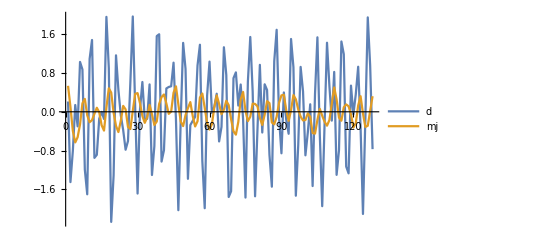

```mathematica
ListPlot[{d,Partition[Riffle[Range[n], mj],2]}, Joined->True, PlotRange->All, PlotLegends->{"d", "mj"}]
```

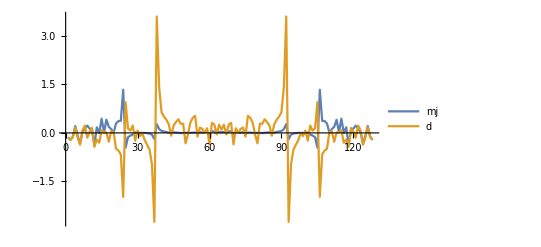

```mathematica
ListPlot[{Partition[Riffle[Range[n], Re[Fourier[mj]]], 2],Partition[Riffle[Range[n], Re[Fourier[d]]], 2]}, Joined->True, PlotRange->All, PlotLegends->{"mj", "d"}]
```

```mathematica
h = 1/(√n)Fourier[mj]/Fourier[d]
```

{0.0883883+0. ⅈ,0.0877963+0.00864718 ⅈ,0.0860352+0.0171135 ⅈ,0.0831494+0.0252231 ⅈ,0.0792117+0.0328106 ⅈ,0.0743205+0.0397252 ⅈ,0.0685972+0.0458352 ⅈ,0.0621822+0.0510316 ⅈ,0.0552308+0.0552308 ⅈ,0.0479084+0.0583765 ⅈ,0.0403855+0.0604411 ⅈ,0.0328327+0.0614256 ⅈ,0.0254158+0.0613592 ⅈ,0.018291+0.0602975 ⅈ,0.0116006+0.0583202 ⅈ,0.00546905+0.0555282 ⅈ,2.75993×10^-18+0.0520395 ⅈ,-0.00472616+0.0479855 ⅈ,-0.00865388+0.043506 ⅈ,-0.0117532+0.0387451 ⅈ,-0.0140196+0.0338463 ⅈ,-0.015473+0.028948 ⅈ,-0.0161562+0.0241795 ⅈ,-0.016132+0.0196569 ⅈ,-0.0154807+0.0154807 ⅈ,-0.014296+0.0117325 ⅈ,-0.0126818+0.00847368 ⅈ,-0.0107473+0.00574454 ⅈ,-0.00860362+0.00356374 ⅈ,-0.00635952+0.00192914 ⅈ,-0.00411754+0.000819029 ⅈ,-0.00197079+0.000194106 ⅈ,2.30239×10^-18+3.07169×10^-18 ⅈ,0.00172875+0.000170267 ⅈ,0.0031657+0.000629696 ⅈ,0.00427832+0.00129781 ⅈ,0.00505162+0.00209245 ⅈ,0.0054876+0.00293318 ⅈ,0.00560424+0.00374463 ⅈ,0.00543371+0.00445933 ⅈ,0.00502021+0.00502021 ⅈ,0.00441736+0.00538257 ⅈ,0.00368526+0.00551539 ⅈ,0.00288746+0.00540206 ⅈ,0.00208785+0.0050405 ⅈ,0.00134765+0.0044426 ⅈ,0.000722661+0.00363306 ⅈ,0.000260787+0.00264782 ⅈ,-5.48152×10^-18+0.0015319 ⅈ,-0.0000331927+0.000337012 ⅈ,0.000175268-0.000881133 ⅈ,0.000626588-0.00206558 ⅈ,0.0013093-0.00316093 ⅈ,0.00220001-0.00411593 ⅈ,0.00326468-0.00488594 ⅈ,0.00446035-0.00543496 ⅈ,0.00573728-0.00573728 ⅈ,0.00704128-0.00577863 ⅈ,0.00831636-0.00555682 ⅈ,0.00950729-0.00508175 ⅈ,0.0105622-0.00437501 ⅈ,0.0114349-0.00346875 ⅈ,0.0120873-0.00240431 ⅈ,0.0124905-0.00123021 ⅈ,0.0126269+0. ⅈ,0.0124905+0.00123021 ⅈ,0.0120873+0.00240431 ⅈ,0.0114349+0.00346875 ⅈ,0.0105622+0.00437501 ⅈ,0.00950729+0.00508175 ⅈ,0.00831636+0.00555682 ⅈ,0.00704128+0.00577863 ⅈ,0.00573728+0.00573728 ⅈ,0.00446035+0.00543496 ⅈ,0.00326468+0.00488594 ⅈ,0.00220001+0.00411593 ⅈ,0.0013093+0.00316093 ⅈ,0.000626588+0.00206558 ⅈ,0.000175268+0.000881133 ⅈ,-0.0000331927-0.000337012 ⅈ,-5.48152×10^-18-0.0015319 ⅈ,0.000260787-0.00264782 ⅈ,0.000722661-0.00363306 ⅈ,0.00134765-0.0044426 ⅈ,0.00208785-0.0050405 ⅈ,0.00288746-0.00540206 ⅈ,0.00368526-0.00551539 ⅈ,0.00441736-0.00538257 ⅈ,0.00502021-0.00502021 ⅈ,0.00543371-0.00445933 ⅈ,0.00560424-0.00374463 ⅈ,0.0054876-0.00293318 ⅈ,0.00505162-0.00209245 ⅈ,0.00427832-0.00129781 ⅈ,0.0031657-0.000629696 ⅈ,0.00172875-0.000170267 ⅈ,2.30239×10^-18-3.07169×10^-18 ⅈ,-0.00197079-0.000194106 ⅈ,-0.00411754-0.000819029 ⅈ,-0.00635952-0.00192914 ⅈ,-0.00860362-0.00356374 ⅈ,-0.0107473-0.00574454 ⅈ,-0.0126818-0.00847368 ⅈ,-0.014296-0.0117325 ⅈ,-0.0154807-0.0154807 ⅈ,-0.016132-0.0196569 ⅈ,-0.0161562-0.0241795 ⅈ,-0.015473-0.028948 ⅈ,-0.0140196-0.0338463 ⅈ,-0.0117532-0.0387451 ⅈ,-0.00865388-0.043506 ⅈ,-0.00472616-0.0479855 ⅈ,2.75993×10^-18-0.0520395 ⅈ,0.00546905-0.0555282 ⅈ,0.0116006-0.0583202 ⅈ,0.018291-0.0602975 ⅈ,0.0254158-0.0613592 ⅈ,0.0328327-0.0614256 ⅈ,0.0403855-0.0604411 ⅈ,0.0479084-0.0583765 ⅈ,0.0552308-0.0552308 ⅈ,0.0621822-0.0510316 ⅈ,0.0685972-0.0458352 ⅈ,0.0743205-0.0397252 ⅈ,0.0792117-0.0328106 ⅈ,0.0831494-0.0252231 ⅈ,0.0860352-0.0171135 ⅈ,0.0877963-0.00864718 ⅈ}

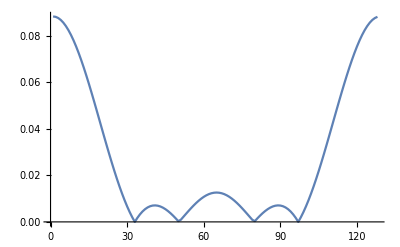

```mathematica
ListPlot[Partition[Riffle[Range[n], Abs[h]], 2],Joined->True]
```

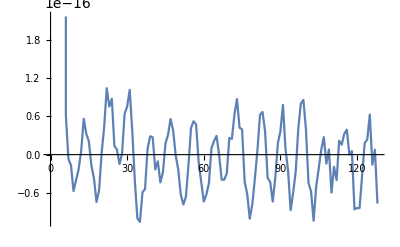

```mathematica
iH = Partition[Riffle[Range[n], Re[InverseFourier[h]]], 2];
ListPlot[iH,Joined->True]
```

```mathematica
l = Table[0, 128];

l[[1]] = d[[3]];
l[[2]] = d[[4]];
l[[3]] = d[[5]];
l[[n-1]] = d[[1]];
l[[n]] = d[[2]];

ll = Partition[Riffle[Range[n], l], 2];
```

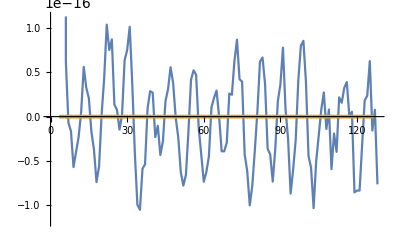

```mathematica
ListPlot[{iH, ll}, Joined -> {True, False}]
```